```mathematica
(* MA39110 / Assignment 5 / 16MA20053 / NER ROHIT *)
ClearAll["Global`*"];
```

```mathematica
Thomas[a_,b_,c_,d_]:=Module[{c1=Range[Length[c]],d1=Range[Length[d]],x=Range[Length[b]]},
c1[[1]]=c[[1]]/b[[1]]; d1[[1]]=d[[1]]/b[[1]];
Do[
If[i≠Length[d],c1[[i]]=c[[i]]/(b[[i]]-a[[i-1]]*c1[[i-1]])];
d1[[i]]=(d[[i]]-a[[i-1]]*d1[[i-1]])/(b[[i]]-a[[i-1]]*c1[[i-1]]);
,{i,2,Length[d]}];
x[[Length[b]]]=d1[[Length[b]]];
Do[
x[[i]]=d1[[i]]-c1[[i]]*x[[i+1]];
,{i,Length[b]-1,1,-1}];
x];
Model[n0_]:=Module[{n=n0},
x0=0;xf=1;h=(xf-x0)/n;
y0=0;yf=0;
A=Table[0,{x,1,n-1},{y,1,n-1}];
X=Table[x0+x*h,{x,1,n-1}];
XT=Table[x0+x*h,{x,0,n}];
B=Table[0,{x,1,n-1}];
eps=0.0001;
PLT={};
(*Initial Approximation: Parabola passing through the points (x0,y0) and (xn,yn).*)
y[x_]=x(1-x);
Y=Table[x*0,{x,1,n+1}];
Y0=Y;
YT=Y;
c=1;
While[{
Y=YT;
For[i=1,i<n,i++,
{
im=i+1;
A[[i,i]]=-2/h^2;
B[[i]]=-Y[[im]]^2+2;
If[i≠1,A[[i,i-1]]=1/h^2+Y[[im]]/(2h)];
If[i≠n-1,A[[i,i+1]]=1/h^2-Y[[im]]/(2h)];
}];
c=c+1;
YT=N[Flatten[{{y0},Thomas[Diagonal[A,-1],Diagonal[A],Diagonal[A,1],B],{yf}}]];
AppendTo[PLT,ListPlot[Transpose[{XT,YT}],PlotStyle->{Red,Green,Blue,Black}[[Mod[c,4]]]]];
};N[Max[Abs[YT-Y]]]>eps];
Print[c];
PLT[[c-1]]=ListLinePlot[Transpose[{XT,YT}],PlotStyle->Black];
Show[PLT[[1;;;;1]],PlotRange->Automatic]
];
```

5

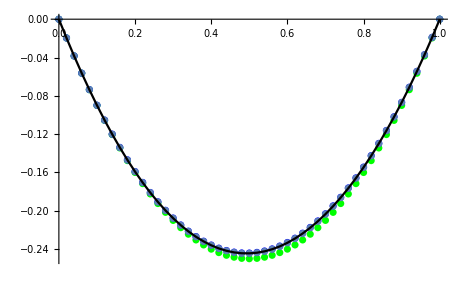

```mathematica
Model[50]
```